### Some checks for the fortran code

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
BohrinAngstrom=0.529177210903;
AngstrominBohr = 1/0.529177210903;
HartreePerMHz=6.579683920502*10^9;
MHzPerHartree = 1/HartreePerMHz;
nkinHartree=3.1668115634556 10^-15;
amu=(1.66053906660 10^-27)/(9.1093837015 10^-31);
mLi7=amu 7.01600455000;
μLi7=mLi7/2;
massRb87 = 86.909180527*amu;
massRb85 =84.911789738*amu;
μRb87 = massRb87/2;
μRb85 = massRb85/2;
Off[ClebschGordan::phy]
Off[General::munfl]
```

```mathematica
C6 = 0.2270032*10^8;
C8 = 0.7782886 *10^9;
C10 = 0.2868869*10^11;
Cvals={C6 invcminHartree AngstrominBohr^6,C8 invcminHartree AngstrominBohr^8,C10 invcminHartree AngstrominBohr^10}
```

{4710.22,576696.,7.59128×10^7}

```mathematica
βRb87=Select[β/.NSolve[(-C6*AngstrominBohr^6*invcminHartree)/β^6-(C8*AngstrominBohr^8*invcminHartree)/β^8-(C10*AngstrominBohr^10*invcminHartree)/β^10==-1/(2 μRb87 β^2),β],Positive][[1]]
```

165.464

```mathematica
BohrinRb87vdw = 1/βRb87
Rb87vdwinHartree = 1/(2 μRb87 βRb87^2);
HartreeinRb87vdw = 1/Rb87vdwinHartree
```

0.00604361

4.33743×10^9

```mathematica
C6vdw = (2 μRb87)/βRb87^4(C6*invcminHartree*AngstrominBohr^6)
C8vdw = (2 μRb87)/βRb87^6(C8*invcminHartree*AngstrominBohr^8)
C10vdw = (2 μRb87)/βRb87^8(C10*invcminHartree*AngstrominBohr^10)
```

0.995527

0.00445197

0.0000214049

```mathematica
Cvalsvdw={C6vdw,C8vdw,C10vdw};
```

```mathematica
Rb87vlr[r_]:= -C6vdw/r^6-C8vdw/r^8-C10vdw/r^10(*-C26vdw/r^26*);
```

```mathematica
VLongRange[μ_,l_,Cvals_,r_]:=-Cvals[[1]]/r^6-Cvals[[2]]/r^8-Cvals[[3]]/r^10+(l(l+1))/(2μ r^2)
```

```mathematica
Lmax=4;
χplus[L_,R_]:=√R BesselJ[-1/4(2L+1),1/(2 R^2)];
χminus[L_,R_]:=√R BesselJ[1/4(2L+1),1/(2 R^2)];
χmprime[L_,r_]:=(-L r^2 BesselJ[1/4 (1+2 L),1/(2 r^2)]+BesselJ[1/4 (5+2 L),1/(2 r^2)])/r^(5/2);
χpprime[L_,r_]:=((1+L) r^2 BesselJ[1/4 (-1-2 L),1/(2 r^2)]+BesselJ[1/4 (3-2 L),1/(2 r^2)])/r^(5/2);
ksqr[ϵ_,l_,r_]:=ϵ-VLongRange[1/2,l,Cvalsvdw,r];
BC1[ϵ_,l_,r_]=Simplify[Evaluate[(ksqr[ϵ,l,r])^(-1/4)]];
BC2[ϵ_,l_,r_]=Simplify[Evaluate[D[(ksqr[ϵ,l,r])^(-1/4),r]]];
```

```mathematica
ϵtest=0.0;
rx=0.1;
rf=80/βRb87;
nr=300;
αsol=Flatten[Table[NDSolve[{α''[r]+ksqr[ϵtest,l,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,l,rx],α'[rx]==BC2[ϵtest,l,rx]},α,{r,rx,rf}],{l,0,Lmax}]];
αfun=Table[α/.αsol[[i]],{i,1,Length[αsol]}];
rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(αfun[[ltest+1]][rp])^-2/.αsol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,Lmax}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,Lmax}];
```

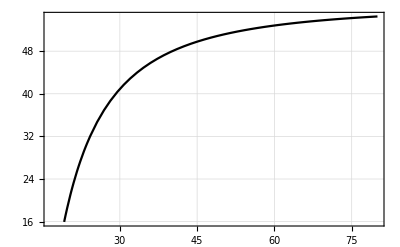

```mathematica
Plot[phaseintfun[[1]][r/βRb87],{r,rx βRb87,rf βRb87},Frame->True,GridLines->Automatic]
```

```mathematica
phaseintfun[[1]][rx]
```

0.

```mathematica
α0=α/.αsol[[1]]
```

InterpolatingFunction[…]

```mathematica
α0p=α0'
```

InterpolatingFunction[…]

```mathematica
α0[rx] √βRb87
```

0.358647

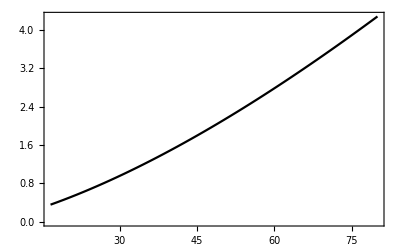

```mathematica
mp1=Plot[α0[R/βRb87] √βRb87,{R,rx βRb87,rf βRb87},Frame->True]
```

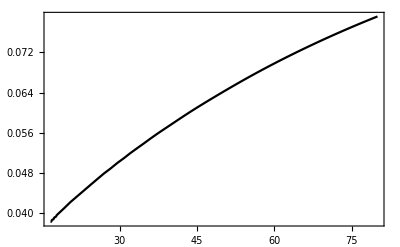

```mathematica
mp2=Plot[α0p[R/βRb87]/√βRb87,{R,rx βRb87,rf βRb87},Frame->True,Axes->False]
```

```mathematica
data1=Import["/Users/niravmehta/Documents/GitHub/LiScattering/fort.101"];
```

```mathematica
af1=Transpose[{data1ᵀ[[1]],data1ᵀ[[2]]}];
af1p=Transpose[{data1ᵀ[[1]],data1ᵀ[[3]]}];
fp1=ListPlot[af1,Joined->True,PlotMarkers->None,PlotStyle->{Red,Thick},Frame->True];
fp2=ListPlot[af1p,Joined->True,PlotMarkers->None,PlotStyle->{Red,Thick},Frame->True];
```

```mathematica
Show[mp1,fp1]
```

-Graphics-

```mathematica
Show[mp2,fp2(*,PlotRange->{{16,20},{0.038,0.042}}*)]
```

-Graphics-

```mathematica
N[Pi,30]
```

3.14159265358979323846264338328

```mathematica
J0table=Table[{x,BesselJ[0,x]},{x,rx βRb87,rf βRb87,.1}];
Y0table=Table[{x,BesselY[0,x]},{x,rx βRb87,rf βRb87,.1}];
chimtable=Table[{x,χminus[0,x/βRb87]},{x,rx βRb87,rf βRb87,.1}];
chimptable=Table[{x,χmprime[0,x/βRb87]/βRb87},{x,rx βRb87,rf βRb87,.1}];
```

```mathematica
(*fJYdata=Transpose[Import["/Users/niravmehta/Documents/GitHub/LiScattering/fort.100"]];*)
fchimdata=Transpose[Import["/Users/niravmehta/Documents/GitHub/LiScattering/fort.100"]];
```

```mathematica
pfJY=ListPlot[{Transpose[{fJYdata[[1]],fJYdata[[2]]}],Transpose[{fJYdata[[1]],fJYdata[[3]]}]},PlotMarkers->None,Joined->True,PlotStyle->Red,Frame->True];
```

```mathematica
pfchim=ListPlot[{Transpose[{fchimdata[[1]],fchimdata[[2]]}](*,Transpose[{fchimdata[[1]]βRb87,fchimdata[[3]]/βRb87}]*)},PlotMarkers->None,Joined->True,PlotStyle->Red,Frame->True];
pfchimp=ListPlot[Transpose[{fchimdata[[1]],fchimdata[[3]]/βRb87}],PlotMarkers->None,Joined->True,PlotStyle->Red,Frame->True];
```

```mathematica
pJY=ListPlot[{J0table,Y0table},Joined->True,PlotMarkers->False,Frame->True,PlotStyle->Black];
pchim=ListPlot[chimtable,Joined->True,PlotMarkers->False,Frame->True,PlotStyle->Black];
pchimp=ListPlot[chimptable,Joined->True,PlotMarkers->False,Frame->True,PlotStyle->Black];
```

```mathematica
Show[pchim,pfchim]
```

-Graphics-

```mathematica
Show[pchimp,pfchimp,Axes->None]
```

-Graphics-

```mathematica
Show[pfJY,pJY]
```

-Graphics-

Need to make a grid that is most efficient.

The local wavelength is

λ=(2π)/k=(2π)/(√(2μ (E-V_lr(r)))≈(2π)/(√(2μ (E+C_6/r^6)))

At zero energy this is simply

λ(r)≈(2π r^3)/(√(2μ C_6))

So we want λ(r)∝r_(i+1)-r_i=Δr/Δi, which is the slope of the r(i) curve.  In other words

Or

ⅆr=A r^3 ⅆi

ⅆr/A r^-3=ⅆi

1/A(r^-2/-2)=i

-1/(2A)=i r^2

-1/(2A)(r_2^-2-r_1^-2)=N

1/(2A)(r_1^-2-r_2^-2)=N

r_max-r_min=A/4(r_max^4-r_min^4)

```mathematica
Ntot=10;Rmin=2;Rmax=40;
Table[Rmin+((i-1)/(Ntot-1))(Rmax-Rmin),{i,1,Ntot}]
```

{2,56/9,94/9,44/3,170/9,208/9,82/3,284/9,322/9,40}

```mathematica
gridpoint[γ_,Rmin_,Rmax_,Ntot_,i_]:=Rmin+((i-1)/(Ntot-1))^γ(Rmax-Rmin)
```

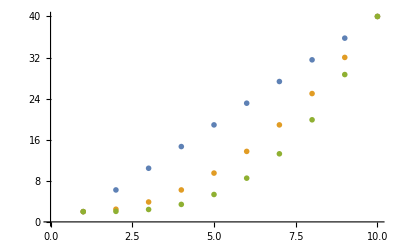

```mathematica
ListPlot[{Table[{i,gridpoint[1,Rmin,Rmax,Ntot,i]},{i,1,Ntot}],Table[{i,gridpoint[2,Rmin,Rmax,Ntot,i]},{i,1,Ntot}],Table[{i,gridpoint[3,Rmin,Rmax,Ntot,i]},{i,1,Ntot}]}]
```